## Parameters of the system

```mathematica
x=AbsoluteTime[];
Clear[L,upspins,downspins,dim,Jxy,Jz,Ε,defectsite,alpha,JJxy,JJz];
L=18;
upspins=L/3;
downspins=L-upspins;
dim=L! /(upspins! downspins!);
(*NN*)
Jxy=1;
Jz=0.47;
alpha=0;
(*NNN*)
JJxy=1;
JJz=0;
(*BASIS*)
Clear[onebasisvector,basis];
onebasisvector=Flatten[{Table[1,{k,1,upspins}],Table[0,{k,1,downspins}]}];
basis=Permutations[onebasisvector];
```

## Preparation to take advantage of symmetries

Symmetries include:
1 )  The Hamiltonian is symmetric, and thus once a basis vector i is associated with a basis vector j, the basis vector j does then not need to be check for whether or not it is associated with i. 
2 ) A basis vector behaves in the same way as its mirrored version for the diagonals, and in a similar fashion for its off diagonals, i.e. H[i,i] = H[mirror[i],mirror[i]], H[i,j] = H[mirror[i],mirror[j]]
Here reversed or pair refers to the mirror of a basis vector.

```mathematica
Reversedbasis=Map[Reverse,basis];
Findpair[i_]:=Module[{paired},
Do[If[basis[[i]]==Reversedbasis[[j]],{paired=j,Break[]}],{j,1,dim}];
Return[paired]
]
iterlist=Range[dim];
pairlist =Map[Findpair,Range[dim]];
symmetricbasisv={};
checkforsym=pairlist-iterlist;
Do[If[checkforsym[[i]]==0,symmetricbasisv=Append[symmetricbasisv,iterlist[[i]]]],{i,1,dim}];

(*Making a pairless list*)

pairless={};
While[Length[iterlist]>0,
pairless=Append[pairless,iterlist[[1]]];
iterlist=DeleteCases[iterlist,Alternatives @@ {iterlist[[1]],pairlist[[iterlist[[1]]]]}]]
```

```mathematica
(*In these lists is put, at the index of the pairless basis, the value of k associated with position j. Only the first association is put in, and there are obviously no mirror terms. i.e. if basisv 2 at position j=3 is associated with basisv 21, then this list has a 0 at the index position[21][j], this is what is meant by only the first association*)
```

```mathematica
OffDiagNNkey=ConstantArray[ConstantArray[0,L-1],Length[pairless]];
OffDiagNNNkey=ConstantArray[ConstantArray[0,L-2],Length[pairless]];
(*key below tells what factor of alpha JJz/4 each HH[[i,i]] has added to it, as a result of comparing all HH[[i,j]],HH[[i,j+2]]*)
DiagNNNkey=ConstantArray[0,Length[pairless]];
```

```mathematica
(*Lists used to ensure that if H[i,j] is known, H[j,i] is not computed*)
Associatedvectors=ConstantArray[{},dim];
Associatedvectors2=ConstantArray[{},dim];
```

```mathematica
Clear[HH];
HH=ConstantArray[ConstantArray[0,dim],dim];//AbsoluteTiming
```

{0.673211,Null}

## Functions for initializing Hamiltonian for initial α

```mathematica
NN[i_,j_]:=Module[{tempbasisv={2},t=pairlist[[i]],posi=Position[pairless,i][[1,1]]},

If[basis[[i,j]]==basis[[i,j+1]],{HH[[i,i]]+=Jz/4,HH[[t,t]]+=Jz/4},{HH[[i,i]]-=Jz/4,HH[[t,t]]-=Jz/4}];

(*Off Diag*)
If[basis[[i,j]]==1 && basis[[i,j+1]]==0,tempbasisv=ReplacePart[ReplacePart[basis[[i]],j-> 0],j+1-> 1]];

If[basis[[i,j]]==0 && basis[[i,j+1]]==1,tempbasisv=ReplacePart[ReplacePart[basis[[i]],j-> 1],j+1-> 0]];

If[tempbasisv[[1]]≠2 && !(MemberQ[Associatedvectors[[i]],tempbasisv]),Do[If[tempbasisv==basis[[k]],{HH[[i,k]]=Jxy/2,HH[[k,i]]=Jxy/2,HH[[t,pairlist[[k]]]]=Jxy/2,HH[[pairlist[[k]],t]]=Jxy/2,Associatedvectors[[k]]=Append[Associatedvectors[[k]],basis[[i]]],OffDiagNNkey[[posi,j]]=k,Break[]}],{k,i+1,dim}]];
]
```

```mathematica
NNN[i_,j_]:=Module[{tempbasisv2={2},t=pairlist[[i]],posi=Position[pairless,i][[1,1]]},

(*Diag*)
If[basis[[i,j]]==basis[[i,j+2]],{HH[[i,i]]+=alpha JJz/4,HH[[t,t]]+=alpha JJz/4,DiagNNNkey[[posi]]+=1},{HH[[i,i]]-=alpha JJz/4,HH[[t,t]]-=alpha JJz/4,DiagNNNkey[[posi]]-=1}];
(*Off Diag*)

If[basis[[i,j]]==1 && basis[[i,j+2]]==0,tempbasisv2=ReplacePart[ReplacePart[basis[[i]],j-> 0],j+2-> 1]];

If[basis[[i,j]]==0 && basis[[i,j+2]]==1,tempbasisv2=ReplacePart[ReplacePart[basis[[i]],j-> 1],j+2-> 0]];

If[tempbasisv2[[1]]≠2 && !(MemberQ[Associatedvectors2[[i]],tempbasisv2]), Do[If[tempbasisv2==basis[[k]],{HH[[i,k]]=alpha JJxy/2 , HH[[k,i]]=alpha JJxy/2,HH[[t,pairlist[[k]]]]=alpha JJxy/2 , HH[[pairlist[[k]],t]]=alpha JJxy/2,Associatedvectors2[[k]]=Append[Associatedvectors2[[k]],basis[[i]]],OffDiagNNNkey[[posi,j]]=k,Break[]}],{k,i+1,dim}]];
]
```

```mathematica
(*Hamiltonian generator without L-1 check of each basis from NN term*)
Hamgen[i_,j_]:=NN[i,j]+NNN[i,j];
```

## Function for editing Hamiltonian for new α

```mathematica
(*Below i inputted is a basis vector from a list without pairs (but with symmetric), ipos is i's position in the list without pairs*)
EditNNN[alphanew_,alphaold_,i_]:=Module[{ipos=Position[pairless,i][[1,1]]},
(*Changing Off-Diagonals*)
Map[If[#≠0,{HH[[i,#]]= alphanew JJxy/2 ,HH[[#,i]]= alphanew JJxy/2,HH[[pairlist[[i]],pairlist[[#]]]]= alphanew JJxy/2,HH[[pairlist[[#]],pairlist[[i]]]]= alphanew JJxy/2}]&,OffDiagNNNkey[[ipos]]];

(*Changing Diagonals*)
HH[[i,i]]+=JJz/4(alphanew-alphaold)(DiagNNNkey[[ipos]]);
HH[[pairlist[[i]],pairlist[[i]]]]+=JJz/4(alphanew-alphaold)(DiagNNNkey[[ipos]]);
(*The symmetric basis vectors got changed twice, so need to revert one of the changes*)
(*Map[HH[[#,#]]-=JJz/4(alphanew-alphaold)(DiagNNNkey[[Position[pairless,#][[1,1]]]])&,symmetricbasisv]*)
]

Fixsym[alphanew_,alphaold_]:=
Map[HH[[#,#]]-=JJz/4(alphanew-alphaold)(DiagNNNkey[[Position[pairless,#][[1,1]]]])&,symmetricbasisv]
```

```mathematica
MakeNewHam[alphanew_,alphaold_]:=Module[{},Map[EditNNN[alphanew,alphaold,#]&,pairless];Fixsym[alphanew,alphaold]]
```

## Generating Hamiltonian

```mathematica
AbsoluteTiming[
(*basis does the usual hamiltonian generation for a basis vector, but adds the term which applies NN to the L-1 place of each chain, which was missed in Hamgen since having NN and NNN in one map was probably more efficient*)
basisinfo[i_]:=Map[Hamgen[i,#]&,Range[L-2]]+NN[i,L-1];

Map[basisinfo[#]&,pairless];//AbsoluteTiming
]
(*Some double multiplication ariseing from Associatedvectors2, have to go through and remove associations*)

Correction[j_]:=Module[{},HH[[j,j]]=HH[[j,j]]/2];
Map[Correction[#]&,symmetricbasisv];//AbsoluteTiming

(*77.15 without second break*)
(*58.25 with break*)
```

{88.0008,{88.0008,Null}}

{0.0002345,Null}

```mathematica
OffDiagNNNkey
```

```mathematica
AbsoluteTiming[
Clear[ Energy,Vector];
{Energy,Vector}=Eigensystem[HH];
(*15min 3 seconds*)
(*14min 43 seconds, a=0.8*)
]
(*13.4 list assign*)
(*16.8 the other way*)
```

{458.212,Null}

## Dividing basis vectors into even and odd parity

```mathematica
AbsoluteTiming[
Neven=0;
Nodd=0;
pairlist;
Do[
Do[
If[Abs[Vector[[j]][[i]]]≥1/(√(20 dim)) ,{If[(Vector[[j]][[i]]≥0 && Vector[[j]][[pairlist[[i]]]] ≥ 0) || (Vector[[j]][[i]]≤ 0 && Vector[[j]][[pairlist[[i]]]] ≤  0),{Neven+=1,even[Neven]=j},{Nodd+=1,odd[Nodd]=j}],Break[]}];
,{i,1,Ceiling[dim/2]}]
,{j,1,dim}]
]
```

{13.8206,Null}

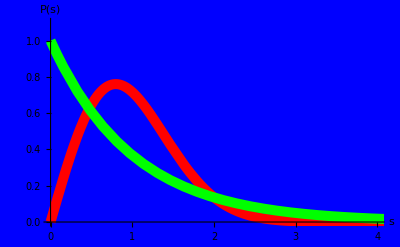

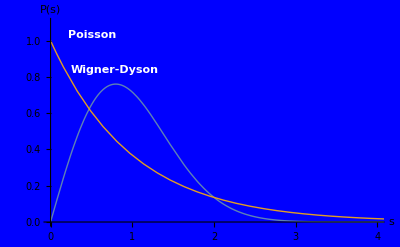

```mathematica
(*For the histogram (?)*)
Clear[spcmin,spcmax,bin,Nofbins];
spcmin=0;
spcmax=8;
bin=0.1;
Nofbins=IntegerPart[(spcmax-spcmin)/bin];
(*Theory curves*)
Clear[WignerDyson,Poisson];
WignerDyson=
Plot[Pi s/2.Exp[-Pi s^2/4.],{s,0,8},PlotRange->{0,1},PlotStyle->{Red,Thickness[0.018]},LabelStyle-> Directive[White,Bold,Medium],AxesLabel-> {"s","P(s)"}];
Poisson=Plot[Exp[-s],{s,0,8},PlotRange-> {0,1},PlotStyle-> {Green,Thickness[0.018]},LabelStyle-> Directive[White,Bold,Medium],AxesLabel-> {"s","P(s)"},PlotLabel->{"Poisson"}];

Show[{WignerDyson,Poisson},PlotRange-> {{0,4},{0,1.1}},Background-> Blue,PlotStyle-> Thick,FrameStyle-> Thick,AxesStyle-> {White,White}]
Plot[{Pi s/2.Exp[-Pi s^2/4.],Exp[-s]},{s,0,8},PlotRange-> {{0,4},{0,1.1}},AxesLabel-> {"s","P(s)"},PlotLabels->Placed[{"Wigner-Dyson","Poisson"},Above],PlotStyle-> Thick,LabelStyle-> Directive[White,Bold,Medium],Background-> Blue,PlotStyle->Thickness[0.018]]
```

```mathematica
AbsoluteTiming[(*Even eigenstates*)
(*Level spacings of the unfolded spectrum*)
(*Order the eigenvalues*)
Clear[Ener];
Ener=Sort[Table[Energy[[even[k]]],{k,1,Neven}]];
(*Discard some eignevalues*)
Clear[percentage,half,spacing];
percentage=(0.1)Neven;
half=Floor[percentage/2];
(*Compute level spacings for the remaining eigenvalues after unfolding them*)
Do[
Clear[average];
average=(Ener[[half+10j]]-Ener[[half+10(j-1)]])/10;
Do[spacing[i]=(Ener[[half+i]]-Ener[[(half-1)+i]])/average,
{i,1+10(j-1),10j}],
{j,1,Floor[(Neven-percentage)/10]}];
Table[spacing[j],{j,1,10 Floor[(Neven-percentage)]}];
]
```

{0.0559313,Null}

```mathematica
AbsoluteTiming[
(*Histogram even*)
Clear[SPChist,Nhist];
SPChist[1]=spcmin;
Do[SPChist[i+1]=SPChist[i]+bin,{i,1,Nofbins}];
Do[Nhist[j]=0,{j,1,Nofbins}];
Do[
Do[
If[SPChist[j]≤ spacing[k]<SPChist[j+1],Nhist[j]=Nhist[j]+1],
{j,1,Nofbins}],
{k,1,10 Floor[(Neven-percentage)/10]}];
Table[Nhist[j],{j,1,Nofbins}]
]
```

{0.804366,{718,641,647,615,505,506,455,398,368,328,305,270,275,225,220,176,173,169,141,119,120,109,107,95,74,64,65,50,41,37,44,40,33,30,39,18,27,13,20,21,13,10,11,4,7,2,5,5,3,3,4,3,4,5,1,0,2,1,1,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{0.102276,Null}

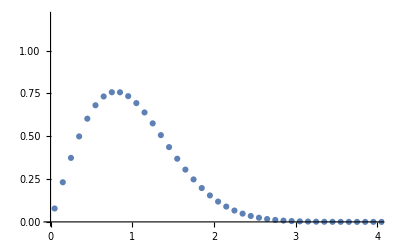

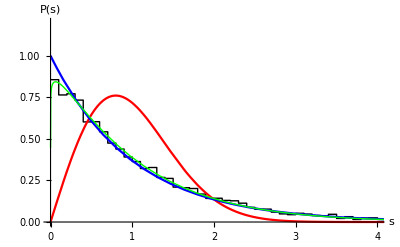

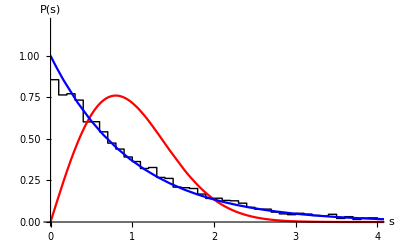

11 26.555216

```mathematica
(*Normalisation*)
AbsoluteTiming[Clear[Norma];
Norma=Sum[(bin) Nhist[j],{j,1,Nofbins}];
Do[Nhist[j]=Nhist[j]/Norma,{j,1,Nofbins}];

Clear[jj,histEven,PlotEven];
jj=0;
histEven={};
Do[
jj+=1;
histEven=Append[histEven,{SPChist[jj],Nhist[jj]}];
histEven=Append[histEven,{SPChist[jj+1],Nhist[jj]}],
{j,1,Nofbins-1}];

PlotEven=
ListPlot[histEven,Joined-> True,PlotRange-> {{0,8},{0,1.2}},PlotStyle-> {Black,Thick},
LabelStyle-> Directive[Black,Bold,Medium],AxesLabel-> {"s","P(s)"}];
(*Tabling Distribution 'points' (x,y)*)

DistTable = Table[{(SPChist[j]+SPChist[j+1])/2,Nhist[j]},{j,1,Nofbins}];
(*Finding best fit for brody distribution*)
Bparam=FindFit[DistTable,(β+1)(Gamma[(β+2)/(β+1)])^(β+1) s^β E^(-(Gamma[(β+2)/(β+1)])^(β+1)  s^(β+1)),β,s];
Brody=
Plot[(β+1)(Gamma[(β+2)/(β+1)])^(β+1) s^β E^(-(Gamma[(β+2)/(β+1)])^(β+1)  s^(β+1))/.Bparam,{s,0,8},PlotRange->{0,1.2},PlotStyle->{Green,Thick},LabelStyle-> Directive[Black,Bold,Medium],AxesLabel-> {"s","P(s)"}];

(*Getting the κ parameter from pg 33 of the santos paper, first get list of spacing points, then evaluate WD at those points*)
spoints=Table[(SPChist[j]+SPChist[j+1])/2,{j,1,Nofbins}];
WDathistbars=Table[1/2 ⅇ^(-(π (s)^2)/4) π (s),{s,spoints}];
WDdist=Table[{spoints[[j]],WDathistbars[[j]]},{j,1,Nofbins}];

(*κ done here*)
κdenom = Sum[WDathistbars[[j]](bin),{j,1,Nofbins}];
distprob=Sum[Nhist[j](bin),{j,1,Nofbins}];
κ=1/κdenom √Sum[(bin(Nhist[j]-WDathistbars[[j]]))^2,{j,1,Nofbins}];
(*0.018 for WD*)

WignerDyson=
Plot[Pi s/2.Exp[-Pi s^2/4.],{s,0,8},PlotRange->{0,1.2},PlotStyle->{Red},LabelStyle-> Directive[White,Bold,Medium],AxesLabel-> {"s","P(s)"}];
Poisson=Plot[Exp[-s],{s,0,8},PlotRange-> {0,1.2},PlotStyle-> {Blue},LabelStyle-> Directive[White,Bold,Medium],AxesLabel-> {"s","P(s)"},PlotLabel->{"Poisson"}];
]
Show[{ListPlot[WDdist]},PlotRange-> {{0,4},{0,1.2}}]
Show[{PlotEven,WignerDyson,Poisson,Brody},PlotRange-> {{0,4},{0,1.2}}]
Show[{PlotEven,WignerDyson,Poisson},PlotRange-> {{0,4},{0,1.2}}]
UnitConvert[Quantity[AbsoluteTime[]-x,"Seconds"],MixedUnit[{"Minutes","Seconds"}]]
```

```mathematica
(*Export["Vectors;L="<>ToString[L]<>";Up="<>ToString[upspins]<>";Jxy="<>ToString[Jxy]<>";Jz="<>ToString[Jz]<>";JJxy="<>ToString[JJxy]<>";JJz="<>ToString[JJz]<>";a="<>ToString[alpha]<>".csv",Vector,OverwriteTarget->True];

Export["Energies;L="<>ToString[L]<>";Up="<>ToString[upspins]<>";Jxy="<>ToString[Jxy]<>";Jz="<>ToString[Jz]<>";JJxy="<>ToString[JJxy]<>";JJz="<>ToString[JJz]<>";a="<>ToString[alpha]<>".csv",Energy,OverwriteTarget->True];*)
```

```mathematica
Table[Nhist[j],{j,1,Nofbins}];
```

```mathematica
Energy;
```

```mathematica
Bparam;
```

```mathematica
κ
```

0.13693

```mathematica
Ener;
```

```mathematica
HH
```

```mathematica
MakeNewHam[0.1,alpha]
MakeNewHam[0.15,0.1]
MakeNewHam[0.2,0.15]

HH
```

{1.5275,0.5875,0.5875,0.5875,0.5875,0.5875,1.0575,0.5875,-0.3525,-0.3525,-0.3525,-0.3525,0.1175,0.5875,-0.3525,-0.3525,-0.3525,0.1175,0.5875,-0.3525,-0.3525,0.1175,0.5875,-0.3525,0.1175,0.5875,0.1175,1.0575,1.0575,0.1175,0.1175,0.1175,0.1175,0.5875,0.1175,-0.8225,-0.8225,-0.8225,-0.3525,0.1175,-0.8225,-0.8225,-0.3525,0.1175,-0.8225,-0.3525,0.1175,-0.3525,0.5875,1.0575,0.1175,0.1175,0.1175,0.5875,0.1175,-0.8225,-0.8225,-0.3525,0.1175,-0.8225,-0.3525,0.1175,-0.3525,0.5875,1.0575,0.1175,0.1175,0.5875,0.1175,-0.8225,-0.3525,0.1175,-0.3525,0.5875,1.0575,0.1175,0.5875,0.1175,-0.3525,0.5875,1.0575,0.5875,0.5875,1.5275}

{1.5275,0.5875,0.5875,0.5875,0.5875,0.5875,1.0575,0.5875,-0.3525,-0.3525,-0.3525,-0.3525,0.1175,0.5875,-0.3525,-0.3525,-0.3525,0.1175,0.5875,-0.3525,-0.3525,0.1175,0.5875,-0.3525,0.1175,0.5875,0.1175,1.0575,1.0575,0.1175,0.1175,0.1175,0.1175,0.5875,0.1175,-0.8225,-0.8225,-0.8225,-0.3525,0.1175,-0.8225,-0.8225,-0.3525,0.1175,-0.8225,-0.3525,0.1175,-0.3525,0.5875,1.0575,0.1175,0.1175,0.1175,0.5875,0.1175,-0.8225,-0.8225,-0.3525,0.1175,-0.8225,-0.3525,0.1175,-0.3525,0.5875,1.0575,0.1175,0.1175,0.5875,0.1175,-0.8225,-0.3525,0.1175,-0.3525,0.5875,1.0575,0.1175,0.5875,0.1175,-0.3525,0.5875,1.0575,0.5875,0.5875,1.5275}

{1.5275,0.5875,0.5875,0.5875,0.5875,0.5875,1.0575,0.5875,-0.3525,-0.3525,-0.3525,-0.3525,0.1175,0.5875,-0.3525,-0.3525,-0.3525,0.1175,0.5875,-0.3525,-0.3525,0.1175,0.5875,-0.3525,0.1175,0.5875,0.1175,1.0575,1.0575,0.1175,0.1175,0.1175,0.1175,0.5875,0.1175,-0.8225,-0.8225,-0.8225,-0.3525,0.1175,-0.8225,-0.8225,-0.3525,0.1175,-0.8225,-0.3525,0.1175,-0.3525,0.5875,1.0575,0.1175,0.1175,0.1175,0.5875,0.1175,-0.8225,-0.8225,-0.3525,0.1175,-0.8225,-0.3525,0.1175,-0.3525,0.5875,1.0575,0.1175,0.1175,0.5875,0.1175,-0.8225,-0.3525,0.1175,-0.3525,0.5875,1.0575,0.1175,0.5875,0.1175,-0.3525,0.5875,1.0575,0.5875,0.5875,1.5275}

```mathematica
HH//MatrixForm
```